### Start choosing the example:

```mathematica
t=2;
beta=0;
A=0.2;
g[x]
```

Log[x]

```mathematica
Data=DataG[t]
```

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m"]
Data=<|"Vertices List"->{1,2},"Adjacency Matrix"->{{0,1},{0,0}},"Entrance Vertices and Currents"->{{1,I1}},"Exit Vertices and Terminal Costs"->{{2,U1}},"Switching Costs"->{}|>;
d2e=Data2Equations[Data/.{I1-> 80, U1-> 0}];
{B,K,c,jj}=GetKirchhoffMatrix[d2e];
```

```mathematica
CriticalCongestionSolver[d2e=Data2Equations[Data/.{I1-> 80, U1-> 0}]]//AbsoluteTiming
CriticalCongestionSolver[d2e]//AbsoluteTiming
```

{80-u1==0,u1≤u1,True}

{0.043653,<|j6→80,j5→0,j3→0,j2→80,j1→0,j4→80,u4→0,jt1→0,jt2→80,jt3→80,jt4→0,u3→0,u6→80,u2→0,u5→80,u1→80|>}

{80-u1==0,u1≤u1,True}

{0.002628,<|j6→80,j5→0,j3→0,j2→80,j1→0,j4→80,u4→0,jt1→0,jt2→80,jt3→80,jt4→0,u3→0,u6→80,u2→0,u5→80,u1→80|>}

```mathematica
NS=And@@{80-u1==0,u1≤u1,True};
Reduce[NS,Reals]//AbsoluteTiming
```

{0.000174,u1==80}

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1-> 80, U1-> 15}]])//AbsoluteTiming
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the critical case equations

Expanding critical rules...

EliminateVarsSimplify for the us

Finished with the us!

Done!

{0.051257,<|u1→95,u2→15,u3→15,u4→15,u5→95,u6→95,j1→0,j2→80,j3→0,j4→80,j5→0,j6→80|>}

```mathematica
(rule=CriticalCongestionSolver2[d2e])//AbsoluteTiming
```

EliminateVarsSimplify for the us

Finished with the us!

Done!

{0.003981,<|u1→95,u2→15,u3→15,u4→15,u5→95,u6→95,j1→0,j2→80,j3→0,j4→80,j5→0,j6→80|>}

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2},Adjacency Matrix→{{0,1},{0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{2,U1}},Switching Costs→{}|>

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: {NonNegative[j5707]&&NonNegative[j5708]&&NonNegative[j5709]&&NonNegative[j5710]&&NonNegative[j5711]&&NonNegative[j5712]&&NonNegative[jt5713]&&NonNegative[jt5714]&&NonNegative[jt5715]&&NonNegative[jt5716]&&j5710==jt5713&&j5709==jt5714&&j5707==jt5715&&j5711==jt5716&&j5707==jt5714&&j5712==jt5713&&j5710==jt5716&&j5708==jt5715&&j5709==80&&u5721==15&&NonNegative[u5717-u5722]&&NonNegative[u5718-u5720]&&-u5719+u5722==0&&-u5718+u5721==0&&(j5710==0||j5707==0)&&(j5711==0||j5708==0)&&(j5712==0||j5709==0)&&(jt5713==0||jt5714==0)&&(jt5715==0||jt5716==0)&&jt5713==0&&(jt5714==0||-u5717+u5722==0)&&(jt5715==0||-u5718+u5720==0)&&jt5716==0&&j5707-j5710-u5717+u5720==0,{j5709→80,u5721→15}}

DataToEquations: It took 1.×10^-6 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.009127,Null}

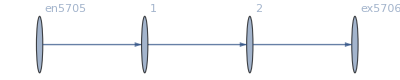

<|j5707→80,j5708→80,j5709→80,j5710→0,j5711→0,j5712→0,jt5713→0,jt5714→80,jt5715→80,jt5716→0,u5717→95,u5718→15,u5719→95,u5720→15,u5721→15,u5722→95|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->80,U1->15}];//Timing
MFGEquations["FG"]
MFGEquations["criticalreduced1"][[2]]//KeySort
```

#### Non-linear case

```mathematica
alpha=0;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u51→17.582}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

EEX: newrules when Head is Equal: {{u51→17.582}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

<|j41→80,j42→80,j43→80,j44→0.,j45→0.,j46→0.,jt47→0.,jt48→80,jt49→80,jt50→0.,u51→17.582,u52→15.,u53→17.582,u54→15.,u55→15.,u56→17.582|>

```mathematica
alpha=0.1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u51→18.1613}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

EEX: newrules when Head is Equal: {{u51→18.1613}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

<|j41→80,j42→80,j43→80,j44→0.,j45→0.,j46→0.,jt47→0.,jt48→80,jt49→80,jt50→0.,u51→18.1613,u52→15.,u53→18.1613,u54→15.,u55→15.,u56→18.1613|>

```mathematica
alpha=0.3;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u51→20.0239}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

EEX: newrules when Head is Equal: {{u51→20.0239}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

<|j41→80,j42→80,j43→80,j44→0.,j45→0.,j46→0.,jt47→0.,jt48→80,jt49→80,jt50→0.,u51→20.0239,u52→15.,u53→20.0239,u54→15.,u55→15.,u56→20.0239|>

```mathematica
alpha=1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,
SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: newrules when Head is Equal: {{u51→95.}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[8.52651×10^-14,ComplexInfinity]

<|j41→80,j42→80,j43→80,j44→0.,j45→0.,j46→0.,jt47→0.,jt48→80,jt49→80,jt50→0.,u51→95.,u52→15.,u53→95.,u54→15.,u55→15.,u56→95.|>

```mathematica
alpha=1.2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u51→378.906}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

EEX: newrules when Head is Equal: {{u51→378.906}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j41→80,j42→80,j43→80,j44→0.,j45→0.,j46→0.,jt47→0.,jt48→80,jt49→80,jt50→0.,u51→378.906,u52→15.,u53→378.906,u54→15.,u55→15.,u56→378.906|>

```mathematica
alpha=1.6;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u51→290058.}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

EEX: newrules when Head is Equal: {{u51→290058.}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j41→80,j42→80,j43→80,j44→0.,j45→0.,j46→0.,jt47→0.,jt48→80,jt49→80,jt50→0.,u51→290058.,u52→15.,u53→290058.,u54→15.,u55→15.,u56→290058.|>

```mathematica
alpha=1.7;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u51→1.5595×10^7}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

EEX: newrules when Head is Equal: {{u51→1.5595×10^7}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j41→80,j42→80,j43→80,j44→0.,j45→0.,j46→0.,jt47→0.,jt48→80,jt49→80,jt50→0.,u51→1.5595×10^7,u52→15.,u53→1.5595×10^7,u54→15.,u55→15.,u56→1.5595×10^7|>

```mathematica
alpha=1.8;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u51→2.40526×10^10}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

EEX: newrules when Head is Equal: {{u51→2.40526×10^10}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j41→80,j42→80,j43→80,j44→0.,j45→0.,j46→0.,jt47→0.,jt48→80,jt49→80,jt50→0.,u51→2.40526×10^10,u52→15.,u53→2.40526×10^10,u54→15.,u55→15.,u56→2.40526×10^10|>

```mathematica
alpha=1.9;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u51→5.6037×10^18}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

EEX: newrules when Head is Equal: {{u51→5.6037×10^18}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j41→80,j42→80,j43→80,j44→0.,j45→0.,j46→0.,jt47→0.,jt48→80,jt49→80,jt50→0.,u51→5.6037×10^18,u52→15.,u53→5.6037×10^18,u54→15.,u55→15.,u56→5.6037×10^18|>

```mathematica
alpha=2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u51→2.2049×10^106}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

EEX: newrules when Head is Equal: {{u51→2.2049×10^106}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j41→80,j42→80,j43→80,j44→0.,j45→0.,j46→0.,jt47→0.,jt48→80,jt49→80,jt50→0.,u51→2.2049×10^106,u52→15.,u53→2.2049×10^106,u54→15.,u55→15.,u56→2.2049×10^106|>

```mathematica
RowReduce@({{0, 0, 0, 1, 0, 0, 0, 0}, {1, -1, 0, 0, -1, 1, 0, 0}, {0, 0, 0, 1, 1, -1, 0, 0}, {-1, 1, 0, 0, 0, 0, -1, 1}, {0, 0, -1, 0, 0, 0, 1, -1}})
```

{{1,-1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,-1,0,0},{0,0,0,0,0,0,1,-1}}

```mathematica
$Context
```

Global`

```mathematica
NDSolve
```

```mathematica
ToString/@{InitRules,RuleBalanceGatheringCurrents,EqEntryIn,RuleEntryOut,TrueEq,RuleExitCurrentsIn,RuleExitValues,EqValueAuxiliaryEdges,EqSwitchingByVertex,EqCompCon,EqBalanceSplittingCurrents,EqCurrentCompCon,EqTransitionCompCon,EqPosJs,EqPosJts,ModuleVarsNames}
```

{InitRules,RuleBalanceGatheringCurrents,EqEntryIn,RuleEntryOut,TrueEq,RuleExitCurrentsIn,RuleExitValues,EqValueAuxiliaryEdges,EqSwitchingByVertex,EqCompCon,EqBalanceSplittingCurrents,EqCurrentCompCon,EqTransitionCompCon,EqPosJs,EqPosJts,ModuleVarsNames}

## ZAnd

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m"]
```

```mathematica
ZAnd[tt,ab||bc]
```

ZAnd[tt,ab]||ZAnd[tt,bc]

```mathematica
False&&True
```

False

## DNF or a new approach to ZAnd

I am working with the structure of the system in triples: {EE, NN, OO}

```mathematica
Clear[DNF]
DNF[{EE_, NN_,OO_?BooleanQ}]:={EE,NN,OO}
DNF[EE_,NN_,OO_]:= 
If[Head[OO]===Equal,With[
{fsol = First@Solve@OO//Quiet},
Print[fsol];
(EE&&NN/.fsol)&&And@@(fsol/.Rule->Equal) ],
Print[OO];
DNF[EE,NN,#]&/@OO]
```

```mathematica
DNF[x==4,x>=0,True]
DNF[x==4,x>=0,False]
```

x==4&&x≥0

False

```mathematica
DNF[x==3,x>=0,xx||xs||xc||xv]
```

xx||xs||xc||xv

xx

xs

xc

xv

xx||xs||xc||xv

```mathematica
DNF[x==5,x>=3&&y>=0,y==5||y-3==35]
```

{y→5}

{y→38}

(x==5&&x≥3&&y==5)||(x==5&&x≥3&&y==38)

```mathematica
{EE,NN,OO}={True,jt15≥0&&jt16≥0&&jt15+jt16≤3&&u10≤2+jt15&&jt15≤u10&&u10≤3+jt16&&1+jt16≤u10&&5≤jt15+jt16+u10≤7&&jt16≤jt15&&jt15≤2+jt16&&4≤2 jt15+jt16≤6&&3≤jt15+2 jt16≤5,(jt15==0||2+jt15-u10==0)&&(jt16==0||3+jt16-u10==0)&&(3-jt15-jt16==0||7-jt15-jt16-u10==0)};
```

```mathematica
DNF[EE,NN,OO]
```

{jt15→0}

{u10→2+jt15}

{jt16→0}

{u10→3+jt16}

{jt16→3-jt15}

{u10→7-jt15-jt16}

((jt16≥0&&jt16≤3&&u10≤2&&0≤u10&&u10≤3+jt16&&1+jt16≤u10&&5≤jt16+u10≤7&&jt16≤0&&0≤2+jt16&&4≤jt16≤6&&3≤2 jt16≤5&&jt15==0)||(jt15≥0&&jt16≥0&&jt15+jt16≤3&&2+jt15≤2+jt15&&jt15≤2+jt15&&2+jt15≤3+jt16&&1+jt16≤2+jt15&&5≤2+2 jt15+jt16≤7&&jt16≤jt15&&jt15≤2+jt16&&4≤2 jt15+jt16≤6&&3≤jt15+2 jt16≤5&&u10==2+jt15))&&((jt15≥0&&jt15≤3&&u10≤2+jt15&&jt15≤u10&&u10≤3&&1≤u10&&5≤jt15+u10≤7&&0≤jt15&&jt15≤2&&4≤2 jt15≤6&&3≤jt15≤5&&jt16==0)||(jt15≥0&&jt16≥0&&jt15+jt16≤3&&3+jt16≤2+jt15&&jt15≤3+jt16&&3+jt16≤3+jt16&&1+jt16≤3+jt16&&5≤3+jt15+2 jt16≤7&&jt16≤jt15&&jt15≤2+jt16&&4≤2 jt15+jt16≤6&&3≤jt15+2 jt16≤5&&u10==3+jt16))&&((jt15≥0&&3-jt15≥0&&u10≤2+jt15&&jt15≤u10&&u10≤6-jt15&&4-jt15≤u10&&5≤3+u10≤7&&3-jt15≤jt15&&jt15≤5-jt15&&4≤3+jt15≤6&&3≤2 (3-jt15)+jt15≤5&&jt16==3-jt15)||(jt15≥0&&jt16≥0&&jt15+jt16≤3&&7-jt15-jt16≤2+jt15&&jt15≤7-jt15-jt16&&7-jt15-jt16≤3+jt16&&1+jt16≤7-jt15-jt16&&jt16≤jt15&&jt15≤2+jt16&&4≤2 jt15+jt16≤6&&3≤jt15+2 jt16≤5&&u10==7-jt15-jt16))

```mathematica
?DNF
```

```mathematica
(BC=Reduce[#,Reals]&/@BooleanConvert[NN&&OO];)//AbsoluteTiming
```

{0.006246,Null}

```mathematica
(NR=NewReduce[NN&&OO];)//AbsoluteTiming
```

{0.055268,Null}

```mathematica
{EE,NN,OO}={True,jt1≥0&&jt15≥0&&jt1≤jt16&&jt16≥0&&jt1≤jt17&&6+jt1≥jt17&&6+jt1≤jt15+jt17&&jt16≤jt17&&jt17≥0&&jt15≥jt18&&jt15+jt17≥jt16+jt18&&jt18≥0&&6+jt1+jt18≥jt15+jt17&&u12≤10+u15&&u12≥u15&&u2≤10+u5&&u2≥u5,(jt16==0||jt15==0)&&(jt18==0||jt17==0)&&(jt16==0||jt15==0)&&(jt18==0||jt17==0)&&(jt16==0||jt15==0)&&(jt18==0||jt17==0)&&(jt16==0||jt15==0)&&(jt18==0||jt17==0)&&(jt1==0||-6-jt1+jt15+jt17==0)&&(jt18==0||jt17==0)&&(jt15==0||jt16==0)&&(jt17==0||jt18==0)&&(jt15==0||jt16==0)&&(jt17==0||jt18==0)&&(jt18==0||jt16==0)&&(-jt1+jt16==0||6+jt1-jt17==0)&&(6+jt1-jt15-jt17+jt18==0||-jt1+jt17==0)&&(jt15==0||jt16==0)&&(jt15==0||10-u2+u5==0)&&(jt16==0||u2-u5==0)&&(jt17==0||10-u12+u15==0)&&(jt18==0||u12-u15==0)};
```

```mathematica
{EE,NN,OO}={True,jt15≥0&&jt16≥0&&jt15+jt16≤3&&u10≤2+jt15&&jt15≤u10&&u10≤3+jt16&&1+jt16≤u10&&5≤jt15+jt16+u10≤7&&jt16≤jt15&&jt15≤2+jt16&&4≤2 jt15+jt16≤6&&3≤jt15+2 jt16≤5,(jt15==0||2+jt15-u10==0)&&(jt16==0||3+jt16-u10==0)&&(3-jt15-jt16==0||7-jt15-jt16-u10==0)};
```

```mathematica
(NR=NewReduce[NN&&OO];)//AbsoluteTiming
(BC=Reduce[#,Reals]&/@BooleanConvert[NN&&OO];)//AbsoluteTiming
```

{0.003493,Null}

{0.004262,Null}

```mathematica
BC=DeleteDuplicates[Sort/@BC];
```

```mathematica
NR=DeleteDuplicates[Sort/@NR];
```

```mathematica
Reduce[Equivalent[NR,BC],Reals]//AbsoluteTiming
```

{0.004615,True}